#### Zad. 1 (dziedziny funkcji, asymptoty + wykres)

```mathematica
(* 1) wyznacz dziedzine, 2) dziedzina + asymptoty + wykres *)
```

```mathematica
(* a *)
```

```mathematica
Log[x/(1-x^2)]
expr=(2x+3)/(4x-3);
Limit[expr,x->3/4,Direction->-1]
Limit[expr,x->3/4,Direction->1]
Limit[expr,x->Infinity]
```

Log[x/(1-x^2)]

∞

-∞

1/2

```mathematica
(* (b) *)
Expand[(x+2)(x-1-Sqrt[3])(x-1+Sqrt[3])]
Sqrt[%]

expr=(x^2+1)/(2x-3);
Limit[expr,x->3/2,Direction->-1]
Limit[expr,x->3/2,Direction->1]
a=Limit[expr/x,x->Infinity]
b=Limit[expr-a x,x->Infinity]
```

-4-6 x+x^3

√(-4-6 x+x^3)

∞

-∞

1/2

3/4

```mathematica
(* (c) *)
Apart[(3-x^2)/(x^2(x+1))]
Sqrt[3/x^2-3/x+2/(1+x)]

expr=(2 x^2+1)/(x^2-4);
Limit[expr,x->-2,Direction->-1]
Limit[expr,x->-2,Direction->1]
Limit[expr,x->2,Direction->-1]
Limit[expr,x->2,Direction->1]
Limit[expr,x->Infinity]
```

3/x^2-3/x+2/(1+x)

√(3/x^2-3/x+2/(1+x))

-∞

∞

∞

-∞

2

6/(1+x)^2+1/(1+x)-5/(3+x)

Log[6/(1+x)^2+1/(1+x)-5/(3+x)]

-∞

∞

-∞

∞

-1

1

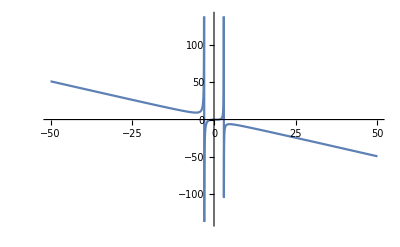

```mathematica
(* (d) *)
Apart[(16-4 x^2)/((x+1)^2(x+3))]
Log[%]
expr=(x^3-x^2-1)/(9-x^2);
Limit[expr,x->-3,Direction->-1]
Limit[expr,x->-3,Direction->1]
Limit[expr,x->3,Direction->-1]
Limit[expr,x->3,Direction->1]
a=Limit[expr/x,x->Infinity]
b=Limit[expr-a x,x->Infinity]
```

#### Zad. 2 (pochodna funkcji)

```mathematica
(* oblicz pochodna funkcji 1) proste wzory, 2) proste wzory + regula rozniczkowania iloczynu/ilorazu, 3) pochodna f. zlozonej + regula rozniczkowania iloczynu/ilorazu *)
(* wykorzystam zadania z innej pracy domowej *)
```

#### Zad. 3 (wzor Taylora)

```mathematica
(* (a) *)
f=x/(3x-2);
Series[f,{x,1,2}]
Normal[%]//Expand
%/.{x->0.9}
f/.{x->0.9}
```

1-2 (x-1)+6 (x-1)^2+O[x-1]^3

9-14 x+6 x^2

1.26

1.28571

```mathematica
(* (b) *)
f=Sqrt[10-x^2];
Series[f,{x,1,2}]
Normal[%]//Expand
%/.{x->0.9}
f/.{x->0.9}
```

3-(x-1)/3-5/27 (x-1)^2+O[x-1]^3

85/27+x/27-(5 x^2)/27

3.03148

3.0315

```mathematica
(* (c) *)
f=Log[(x-1)/(3-x)];
Series[f,{x,2,2}]
Normal[%]//Expand
%/.{x->2.1}
f/.{x->2.1}
```

2 (x-2)+O[x-2]^3

-4+2 x

0.2

0.200671

```mathematica
(* (d) *)
f=ArcSin[x];
Series[f,{x,0,3}]
Normal[%]//Expand
%/.{x->0.1}
f/.{x->0.1}
```

x+x^3/6+O[x]^4

x+x^3/6

0.100167

0.100167